## Collagen Numerical Eigensystems Analysis

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["./results/Parameters","Grid"]
```

/home/hemant/Documents/PhD/WorkspaceCollagen/Workspace/collagen

| 
L: | 5.
m: | 10
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.25
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Results of calculated Eigenvectors using GSL C++

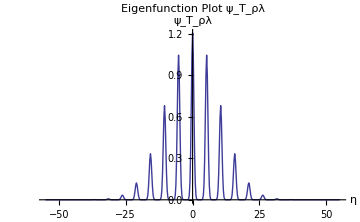
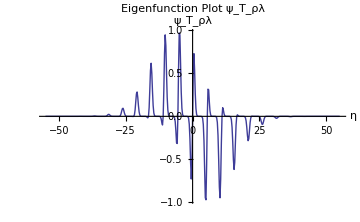
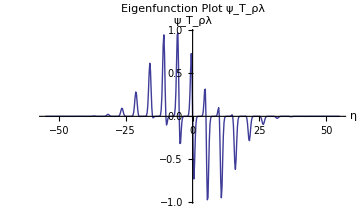
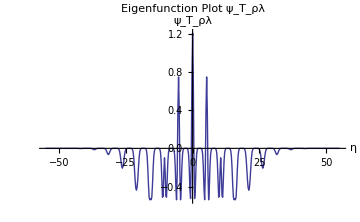

```mathematica
Tρλ0=Import["./logs/TROE_LAMBDA/Phi_roe_lambda0.TROE_LAMBDA","Table"];
Tρλ1=Import["./logs/TROE_LAMBDA/Phi_roe_lambda1.TROE_LAMBDA","Table"];
Tρλ2=Import["./logs/TROE_LAMBDA/Phi_roe_lambda2.TROE_LAMBDA","Table"];
Tρλ3=Import["./logs/TROE_LAMBDA/Phi_roe_lambda3.TROE_LAMBDA","Table"];
Tρλ4=Import["./logs/TROE_LAMBDA/Phi_roe_lambda4.TROE_LAMBDA","Table"];
Tρλ5=Import["./logs/TROE_LAMBDA/Phi_roe_lambda5.TROE_LAMBDA","Table"];

{ListLinePlot[{Tρλ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρλ]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium],
ListLinePlot[{Tρλ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρλ]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium],
ListLinePlot[{Tρλ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρλ]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium],
ListLinePlot[{Tρλ3},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρλ]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium]}
```

Numerical Calculation of Eigenfunctions (Mathematica)

Functions & Eigensystem Calculation

```mathematica
L=5;
m=10;
Δ=L/(2 m)//N;
max=2 m+1;
MAX =(2 m+1)^2;
M=(MAX-1)/2;
```

```mathematica
h0=Partition[Table[Tρλ0[[i,2]],{i,1,Length[Tρλ0],1}],max];
h1=Partition[Table[Tρλ1[[i,2]],{i,1,Length[Tρλ1],1}],max];
h2=Partition[Table[Tρλ2[[i,2]],{i,1,Length[Tρλ2],1}],max];
h3=Partition[Table[Tρλ3[[i,2]],{i,1,Length[Tρλ3],1}],max];

lp0=Flatten[Table[{ Δ i ,Δ j ,h0[[i+m+1,j+m+1]]},{i,-m,m},{j,-m,m}],1];
lp1=Flatten[Table[{ Δ i ,Δ j ,h1[[i+m+1,j+m+1]]},{i,-m,m},{j,-m,m}],1];
lp2=Flatten[Table[{ Δ i ,Δ j ,h2[[i+m+1,j+m+1]]},{i,-m,m},{j,-m,m}],1];
lp3=Flatten[Table[{ Δ i ,Δ j ,h3[[i+m+1,j+m+1]]},{i,-m,m},{j,-m,m}],1];

LP0=ListPlot3D[lp0,ImageSize->Medium,PlotRange->All,AxesLabel -> {η,η',Subscript[ψ̂, 1]},PlotLabel->"Eigenmatrix Plot (ψ̂)_1"];
LP1=ListPlot3D[lp1,ImageSize->Medium,PlotRange->All,AxesLabel -> {η,η',Subscript[ψ̂, 2]},PlotLabel->"Eigenmatrix Plot (ψ̂)_2"];
LP2=ListPlot3D[lp2,ImageSize->Medium,PlotRange->All,AxesLabel -> {η,η',Subscript[ψ̂, 3]},PlotLabel->"Eigenmatrix Plot (ψ̂)_3"];
LP3=ListPlot3D[lp3,ImageSize->Medium,PlotRange->All,AxesLabel -> {η,η',Subscript[ψ̂, 4]},PlotLabel->"Eigenmatrix Plot (ψ̂)_4"];

{LP0,LP1,LP2,LP3}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}